```mathematica
data=NBodySimulation["InverseSquare",{<|"Mass"->1,"Position"->{0,0},"Velocity"->{0,.5}|>,<|"Mass"->1,"Position"->{1,1},"Velocity"->{0,-.5}|>,<|"Mass"->1,"Position"->{0,1},"Velocity"->{0,0}|>},4]
```

NBodySimulationData[3, <4.>]

```mathematica
ParametricPlot3D[Evaluate[data[All,"Position",t]],{t,0,1}]
```

-Graphics3D-

```mathematica
FacialFeatures[CurrentImage[]]
```

```mathematica
{<|"Image"->,"Age"->32,"Gender"->"Male","Emotion"->Indeterminate|>}
```

```mathematica
ResourceFunction["StopCamera"][]
```

[]

```mathematica
WeatherData["Aberdeen", "WindSpeed"]
```

11.16 km/h

```mathematica
Table[n, {n, 10}]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
Select[ Table[n, {n, 100}],PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
Select[ Range[100],PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
Prime[Range[PrimePi[100]]]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
Select[ Range[100],Length[Divisors[#]]==2&]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

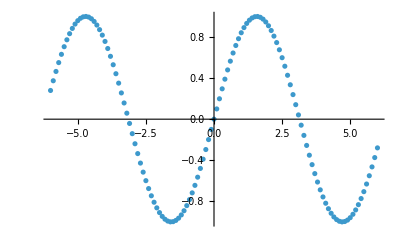

```mathematica
ListPlot[Table[{n, Sin[n]}, {n, -6, 6, 0.1}]]
```

```mathematica
ExampleData[{"TestImage","Couple2"}]
```

-Graphics-

```mathematica
FindTextualAnswer[WikipediaData["Rhinos"], "What the horn of a rhino is made of?"]
```

keratin

```mathematica
Classify["NotablePerson", CurrentImage[]]
```

```mathematica
Entity["Person","FloRida::cyb65"]["Image"]
```

-Graphics-

```mathematica
Entity["Person","FrankOcean::y37b7"]["Image"]
```

-Graphics-

```mathematica
Dataset[EntityValue[Entity["Person","DonaldTrump::6vv3q"],{EntityProperty["Person","FullName"],EntityProperty["Person","BirthDate"],EntityProperty["Person","BirthPlace"]},"PropertyAssociation"]]
```